# Radionchik_S_S Lab2: Символьные вычисления в системе Mathematica

## 1. Выражения

### 1. Придумайте и определите символьное выражение, содержащее не менее трех слагаемых, причем хотя бы одно из них должно быть рациональным выражением. Примените последовательно к нему функции Expand, ExpandAll, Factor, Together, Apart, Cancel, Simplify.

```mathematica
exp = (5x^2 + x +34) 3 / (16 - 3x)^2 + 15(6x^2 + 13) + 17^2
Expand[exp]
ExpandAll[exp]
Factor[exp]
Together[exp]
Apart[exp]
Cancel[exp]
Simplify[exp]
```

289+(3 (34+x+5 x^2))/(16-3 x)^2+15 (13+6 x^2)

484+102/(16-3 x)^2+(3 x)/(16-3 x)^2+90 x^2+(15 x^2)/(16-3 x)^2

484+90 x^2+102/(256-96 x+9 x^2)+(3 x)/(256-96 x+9 x^2)+(15 x^2)/(256-96 x+9 x^2)

(124006-46461 x+27411 x^2-8640 x^3+810 x^4)/(-16+3 x)^2

(124006-46461 x+27411 x^2-8640 x^3+810 x^4)/(-16+3 x)^2

1457/3+90 x^2+1634/(3 (-16+3 x)^2)+163/(3 (-16+3 x))

289+(3 (34+x+5 x^2))/(-16+3 x)^2+15 (13+6 x^2)

484+90 x^2+(3 (34+x+5 x^2))/(16-3 x)^2

### 2. Приведите выражение t1 к общему знаменателю и с помощью функции Numerator определите числитель полученного выражения, обозначив его t2. С помощью функции Collect представьте выражение t2 в виде полинома по измерениям x или y. Определите максимальную степень n одной из переменных. Используйте функции Exponent и Coefficient.

```mathematica
exp = (5x^2 + x +34) 3 / (16 - 3x)^2 + 15(6x^2 + 13) + 17^2
exp = Together[exp]
t2 = Numerator[exp]
t2 = Collect[t2, x]
Exponent[t2, x]
Coefficient[t2, x^Exponent[t2, x]]
```

289+(3 (34+x+5 x^2))/(16-3 x)^2+15 (13+6 x^2)

(124006-46461 x+27411 x^2-8640 x^3+810 x^4)/(-16+3 x)^2

124006-46461 x+27411 x^2-8640 x^3+810 x^4

124006-46461 x+27411 x^2-8640 x^3+810 x^4

4

810

## 2. Производные

### 1. С помощью функции D вычислите производную функции x^n*cos x.

```mathematica
D[x^n Cos[x], x]
```

n x^(-1+n) Cos[x]-x^n Sin[x]

### 2. Вычислите следующие производные: -Graphics-

```mathematica
D[a x^3 + 2  x^2, x]
D[(4x^2-5x+8-3/x), {x,3}]
D[(x^3 y^2+3x^2), {x, 3}, {y, 2}]
```

4 x+3 a x^2

18/x^4

12

### 3. Используя функцию Integrate, вычислите интеграл: -Graphics-

```mathematica
Integrate[1/(x^2 - 1), x]
```

1/2 Log[1-x]-1/2 Log[1+x]

### 4. Вычислите интегралы, затем продифференцируйте полученные выражения и убедитесь в том, что получаемые результаты совпадают с подынтегральными выражениями. -Graphics-

```mathematica
var1 = (x^3) / (x^2+1)
var1 = Integrate[var1, x]
expected1 = Simplify[D[var1, x]]

var2 = 1 / (x^3 +1 )
var2 = Integrate[var2, x]
expected2 = Simplify[D[var2, x]]
```

x^3/(1+x^2)

x^2/2-1/2 Log[1+x^2]

x^3/(1+x^2)

1/(1+x^3)

ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2]

1/(1+x^3)

### 5. Вычислите определенный интеграл. -Graphics-

```mathematica
Integrate[5*x-2*√x+32/x^3, {x,1,4}]
```

259/6

### 6. -Graphics-

```mathematica
N[Integrate[(1+x^4)^(1/3), {x,0,1}],10] (*численное приближение*)
Integrate[(1+x^4)^(1/3),{x,0,1.}]
(*Real numbers entered with just a few digits are generally represented as machine reals*)
```

1.057527732

1.05753

## 3. Системы уравнений

### 1. Используя функцию Solve, решить уравнение -Graphics-

```mathematica
Solve[a x^4+x^2+3==0,x]/. a -> 1/12
(*В Языке Wolfram символ ==(два знака равенства) используется для проверки равенства (true/false)
оператором присваивания " = " - вычисленное значение и оператором отложенного присваивания " := "- невычесленное значение*)
```

{{x→-(√(-1/a-(√(1-12 a))/a))/(√2)},{x→(√(-1/a-(√(1-12 a))/a))/(√2)},{x→-(√(-1/a+(√(1-12 a))/a))/(√2)},{x→(√(-1/a+(√(1-12 a))/a))/(√2)}}

### 2. Найти точное решение системы уравнений: -Graphics-

```mathematica
Solve[x^2+y==1&&y^2-x^2==2, {x,y}]
```

{{x→-ⅈ √(1/2 (-3+√13)),y→1/2 (-1+√13)},{x→ⅈ √(1/2 (-3+√13)),y→1/2 (-1+√13)},{x→-√(1/2 (3+√13)),y→1/2 (-1-√13)},{x→√(1/2 (3+√13)),y→1/2 (-1-√13)}}

### 3. Решить систему уравнений: -Graphics-

```mathematica
NSolve[x^2-y^2==1&&y^3+x==5, {x,y}]
```

{{x→-0.928941-1.39823 ⅈ,y→-0.788459-1.64735 ⅈ},{x→-0.928941+1.39823 ⅈ,y→-0.788459+1.64735 ⅈ},{x→1.78303,y→1.47621},{x→-2.17236,y→1.9285},{x→1.1236-1.05808 ⅈ,y→-0.913899+1.30087 ⅈ},{x→1.1236+1.05808 ⅈ,y→-0.913899-1.30087 ⅈ}}

### 4. Найдите общие решения дифференциальных уравнений, используя функцию DSolve: -Graphics- Самостоятельно задайте граничные условия и найдите соответствующие им частные решения. Постройте их графики.

-Tan[x] y[x]+y'[x]==x

{{y[x]→C[1] Sec[x]+Sec[x] (Cos[x]+x Sin[x])}}

{{y[x]→Sec[x]+Sec[x] (Cos[x]+x Sin[x])}}

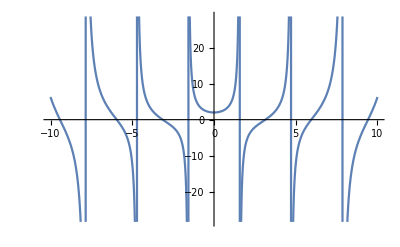

```mathematica
expression = y'[x]-y[x]Tan[x]==x
result =DSolve[expression,y[x],x]
result=result /.C[1] -> 1 (*/. и -> - для замены частей выражения (с1 на 1)*)
Plot[y[x] /. result,{x,-10,10}]
```

Tan[x] y[x]+y'[x]==Sec[x]

{{y[x]→C[1] Cos[x]+Sin[x]}}

{{y[x]→Cos[x]+Sin[x]}}

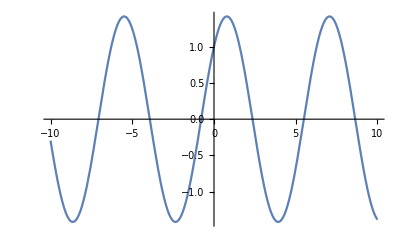

```mathematica
expression = y'[x]+y[x]Tan[x]==1/Cos[x]
result =DSolve[expression,y[x],x]
result=result /.C[1] -> 1
Plot[y[x]/.result,{x,-10,10}]
```

### 5. Самостоятельно выбрав граничные условия, найдите решения дифференциального уравнения в символьном виде: -Graphics- Затем с помощью функции NDSolve найдите численное значение этого уравнения. Интервал изменения x выберете самостоятельно. На одной координатной плоскости постройте графики численного и символьного решений и покажите, что они совпадают.

{{y[x]→-2 ⅇ^(x/2) π (AiryAiPrime[1/4] AiryBi[1/4-x]-AiryAi[1/4-x] AiryBiPrime[1/4])}}

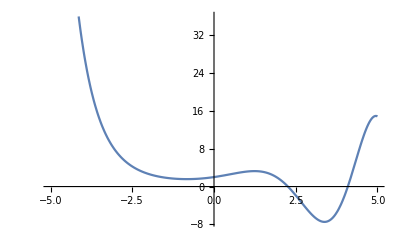

{{y[x]→InterpolatingFunction[…][x]}}

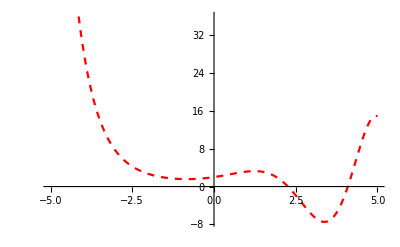

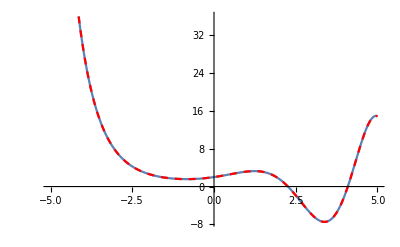

```mathematica
expression = {y''[x]-y'[x]+x y[x]==0, y[0]== 2, y'[0]==1};
solution1 = FullSimplify[ DSolve[expression, y[x], x]]
plot1 = Plot[solution1[[1, 1, 2]], {x, -5, 5}]
solution2 =  NDSolve[expression, y[x], {x, -10, 10}]
plot2 = Plot[solution2[[1, 1, 2]], {x, -5, 5}, PlotStyle-> {Dashed, Red}]
Show[plot1, plot2]
```

## 4. Ограниченные пластинки

### Вариант 3 Пластинка ограничена кривой -Graphics- и прямыми -Graphics- 1.Найти координаты центра масс пластинки. 2. Изобразить пластинку на плоскости xOy и отметить положение ее центра масс. 3. Вычислить моменты инерции пластинки относительно осей Ox, Oy, Oz и показать, что справедливо соотношение lx + ly = lz. -Graphics-

```mathematica
(* вводим ограничения *)
exp1 =x^2
exp2 = 2x+3
exp3 = -x+3

eq1 = exp1==y
eq2 = exp2==y
eq3 = exp3==y
```

x^2

3+2 x

3-x

x^2==y

3+2 x==y

3-x==y

{{x→1/2 (-1-√13),y→1/2 (7+√13)},{x→1/2 (-1+√13),y→1/2 (7-√13)}}

1/2 (-1+√13)

1/2 (7-√13)

{{x→0,y→3}}

0

3

{{x→-1,y→1},{x→3,y→9}}

-1

1

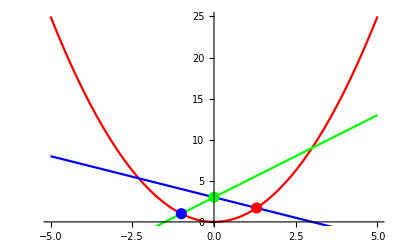

```mathematica
(* Точки пересечения кривых *)
sol1 =Solve[{eq1, eq3}, {x, y}]
x1 = x/.sol1[[2]] (*выбор данных решения*)
y1 = y/.sol1[[2]]

sol2 = Solve[{eq2, eq3}, {x, y}]
x2 = x /. sol2[[1]]
y2 = y/.sol2[[1]]

sol3 = Solve[{eq1, eq2}, {x, y}]
x3 = x /. sol3[[1]]
y3 = y /. sol3[[1]]

Show[Plot[exp1,{x,-5,5},PlotStyle->Red],
Plot[exp2,{x,-5,5},PlotStyle->Green],
Plot[exp3,{x,-5,5},PlotStyle->Blue],Epilog->{PointSize[0.02],Red,Point[{x1,y1}],Green,Point[{x2,y2}],Blue,Point[{x3,y3}]}]
```

1/12 (-1-13 √13)

1/366 (-188+65 √13)

1/915 (2030-221 √13)

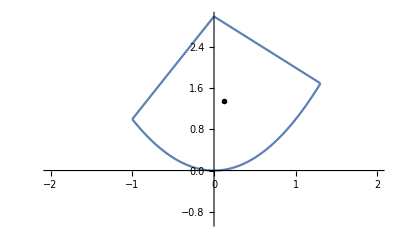

```mathematica
(* Разбиваем пластинки на маленькие кусочки с помощью интегрирования, таким образом находим площадь *)

s =Simplify[Integrate[1, {x, x1, x2}, {y, exp1, exp3}] + Integrate[1, {x, x2, x3}, {y, exp1,  exp2}]]
(* находим положение центра масс *)
xc =Simplify[(1/m)(Integrate[(m/s)x, {x, x1, x2}, {y, exp1, exp3}] + Integrate[(m/s)x, {x, x2, x3}, {y, exp1,  exp2}])]
yc = Simplify[(1/m)(Integrate[(m/s)y, {x, x1, x2}, {y, exp1,exp3}] + Integrate[(m/s)y, {x, x2, x3}, {y, exp1,  exp2}])]
(* Координаты центра масс *)
p1 = Plot[exp1, {x, x1, x3}];
p2= Plot[exp2, {x, x2, x3}];
p3= Plot[exp3, {x, x1, x2}];
Show[p1,p2,p3,PlotRange->{{-2,2},{-1,3}},Epilog->{PointSize[0.01],Point[{xc,yc}]}]
```

```mathematica
(*Момент инерции пластинки*)
ix = Integrate[(m/s)y^2, {x, x1, x2}, {y, exp1, exp3}] + Integrate[(m/s)y^2, {x, x2, x3}, {y, exp1,  exp2}]
iy = Integrate[(m/s)x^2, {x, x1, x2}, {y, exp1, exp3}] + Integrate[(m/s)x^2, {x, x2, x3}, {y,  exp1,  exp2}]
iz=  Integrate[(m/s)(x^2+y^2), {x, x1, x2}, {y, exp1, exp3}] + Integrate[(m/s)(x^2+y^2), {x, x2, x3}, {y,  exp1,  exp2}]

ii = Simplify[ix + iy]
Simplify[ii-iz]
```

(276 m)/(7+91 √13)+(3 (-1037+377 √13) m)/(14+182 √13)

(297 m)/(10 (-1-13 √13))-(117 √13 m)/(10 (-1-13 √13))

(1506 m)/(35+455 √13)+(3 (-2981+1079 √13) m)/(35+455 √13)

(3 (-2479+1079 √13) m)/(35+455 √13)

0